```mathematica
Show[jupiterGraph,saturnGraph,uranusGraph,neptuneGraph,plutoGraph]
```

-Graphics3D-

```mathematica
(*Jupiter*)
jupSemiMajor=QuantityMagnitude[jupiterSemiMajorAxis,"Meters"];
jupSemiMinor = QuantityMagnitude[jupiterSemiMinorAxis,"Meters"];
paraJupx [t_]= jupSemiMajor*Cos[t];
paraJupy[t_]=jupSemiMinor*Sin[t];
jupPlot2D=ParametricPlot[{paraJupx[t],paraJupy[t]},{t,0,10}];
```

```mathematica
(*Saturn*)
```

```mathematica
satSemiMajor=QuantityMagnitude[saturnSemiMajorAxis,"Meters"];
satSemiMinor = QuantityMagnitude[saturnSemiMinorAxis,"Meters"];
paraSatx [t_]= satSemiMajor*Cos[t];
paraSaty[t_]=satSemiMinor*Sin[t];
satPlot2D=ParametricPlot[{paraSatx[t],paraSaty[t]},{t,0,2Pi}];
```

```mathematica
(*Uranus*)
```

```mathematica
uraSemiMajor=QuantityMagnitude[uranusSemiMajorAxis,"Meters"];
uraSemiMinor = QuantityMagnitude[uranusSemiMinorAxis,"Meters"];
paraUrax [t_]= uraSemiMajor*Cos[t];
paraUray[t_]= uraSemiMinor*Sin[t];
uraPlot2D=ParametricPlot[{paraUrax[t],paraUray[t]},{t,0,2Pi}];
```

```mathematica
(*Neptune*)
```

```mathematica
nepSemiMajor=QuantityMagnitude[neptuneSemiMajorAxis,"Meters"];
nepSemiMinor = QuantityMagnitude[neptuneSemiMinorAxis,"Meters"];
paraNepx [t_]= nepSemiMajor*Cos[t];
paraNepy[t_]=nepSemiMinor*Sin[t];
nepPlot2D=ParametricPlot[{paraNepx[t],paraNepy[t]},{t,0,2Pi}];
```

```mathematica
(*Pluto*)
```

```mathematica
pluSemiMajor=QuantityMagnitude[plutoSemiMajorAxis,"Meters"];
pluSemiMinor = QuantityMagnitude[plutoSemiMinorAxis,"Meters"];
paraPlux [t_]= pluSemiMajor*Cos[t];
paraPluy[t_]=pluSemiMinor*Sin[t];
pluPlot2D=ParametricPlot[{paraPlux[t],paraPluy[t]},{t,0,2Pi}];
```

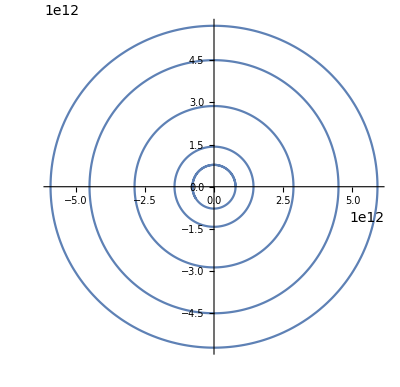

```mathematica
gasGiant2Dparaplot = Show[jupPlot2D,satPlot2D,uraPlot2D,nepPlot2D,pluPlot2D,PlotRange->All]
```